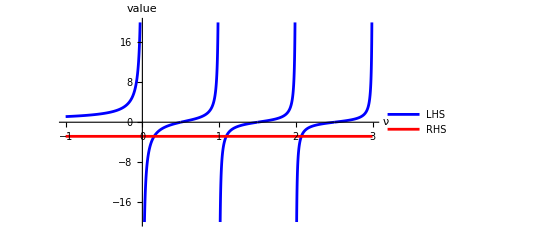

{0.153373,1.09353,2.07237}

Solutions for ν:

{0.153373,1.09353,2.07237}

Relative energies E_r:

{0.806746,2.68705,4.64473}

```mathematica
(* ============================================
   Parameters
   ============================================ *)

g = 1.0;                (* interaction strength *)
hbar = 1.0;             
omega = 1.0;

(* ============================================
   Define functions
   ============================================ *)

lhs[nu_] := Gamma[-nu]/Gamma[1/2 - nu];
rhs = -2^(3/2)/g;

f[nu_] := lhs[nu] - rhs;

(* ============================================
   Plot of both sides
   ============================================ *)

Plot[
 {
  lhs[nu],
  rhs
 },
 {nu, -1, 3},
 PlotRange -> {-20, 20},
 PlotLegends -> {"LHS", "RHS"},
 AxesLabel -> {"ν", "value"},
 PlotStyle -> {Blue, Red}
]

(* ============================================
   Automatic root finding by sign-change
   ============================================ *)

nuGrid = Subdivide[-1, 3, 3000];
fGrid = f /@ nuGrid;

solutions = Reap[
   Do[
    If[
      NumberQ[fGrid[[i]]] && NumberQ[fGrid[[i + 1]]] &&
      fGrid[[i]]*fGrid[[i + 1]] < 0,           (* sign change detected *)
      
      (* isolate root using FindRoot/ bracketing *)
      root = N[nu /. 
         FindRoot[f[nu] == 0, {nu, nuGrid[[i]], nuGrid[[i + 1]]}, 
         Method -> "Brent"]];
      
      Sow[root];
     ],
    {i, 1, Length[nuGrid] - 1}
   ]
 ][[2, 1]];


solutions = DeleteDuplicates[Round[solutions, 10^-10]];
solutions = N[solutions]
Print["Solutions for ν:"];
solutions

(* ============================================
   Energies: E_r = ħ ω (2 ν + 1/2)
   ============================================ *)

energies = hbar*omega*(2 # + 1/2) & /@ solutions;

Print["Relative energies E_r:"];
energies
```

```mathematica
(*total energy for a given (n_cm,ν)*)
Erel[nu_]:=hbar*omega*(2 nu+1/2);
Ecm[n_]:=hbar*omega*(n+1/2);
Etotal[n_,nu_]:=Ecm[n]+Erel[nu];

(*Example:table of first few total energies*)
Table[{n,nusol,Etotal[n,nusol]},{n,0,2},{nusol,solutions}]
```

{{{0,0.153373,1.30675},{0,1.09353,3.18705},{0,2.07237,5.14473}},{{1,0.153373,2.30675},{1,1.09353,4.18705},{1,2.07237,6.14473}},{{2,0.153373,3.30675},{2,1.09353,5.18705},{2,2.07237,7.14473}}}

```mathematica
tableData=Flatten[Table[{n,nu,Etotal[n,nu]},{n,0,2},{nu,solutions}],1];

Grid[Prepend[tableData,{"n","ν","E total"}],Frame->All,Alignment->Center,ItemStyle->Directive[14,Black]]
```

n | ν | E total
0 | 0.153373 | 1.30675
0 | 1.09353 | 3.18705
0 | 2.07237 | 5.14473
1 | 0.153373 | 2.30675
1 | 1.09353 | 4.18705
1 | 2.07237 | 6.14473
2 | 0.153373 | 3.30675
2 | 1.09353 | 5.18705
2 | 2.07237 | 7.14473

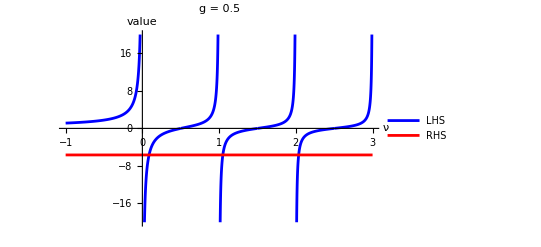
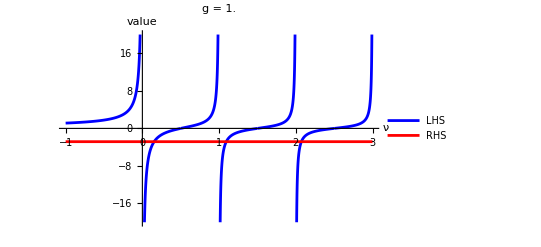
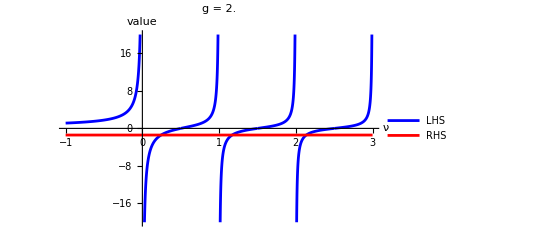
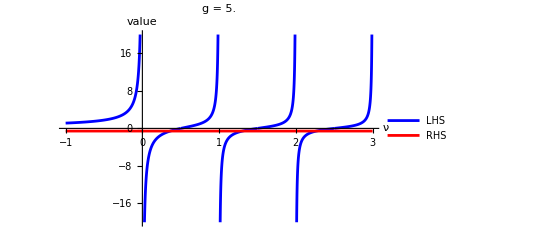
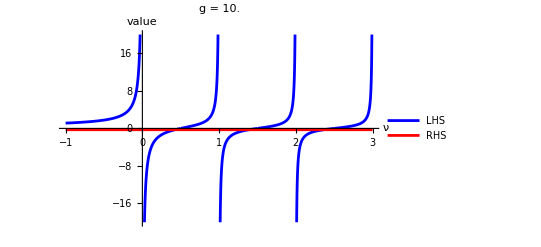
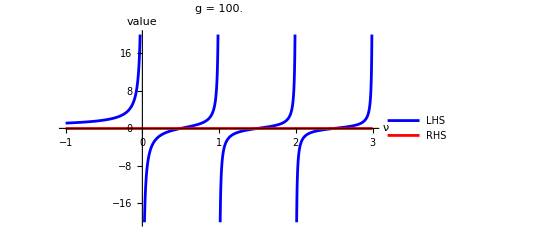

```mathematica
gValues={0.5,1.0, 2.0,5.0,10.0,100.0};

plots=Table[Module[{gval=gv,rhsFunc},rhsFunc=-2^(3/2)/gval;
Plot[{Gamma[-nu]/Gamma[1/2-nu],rhsFunc},{nu,-1,3},PlotRange->{-20,20},PlotLegends->Placed[{"LHS","RHS"},{0.8,0.8}],AxesLabel->{"ν","value"},PlotLabel->Style["g = "<>ToString[gval],14,Bold],PlotStyle->{Blue,Red}]],{gv,gValues}]
```

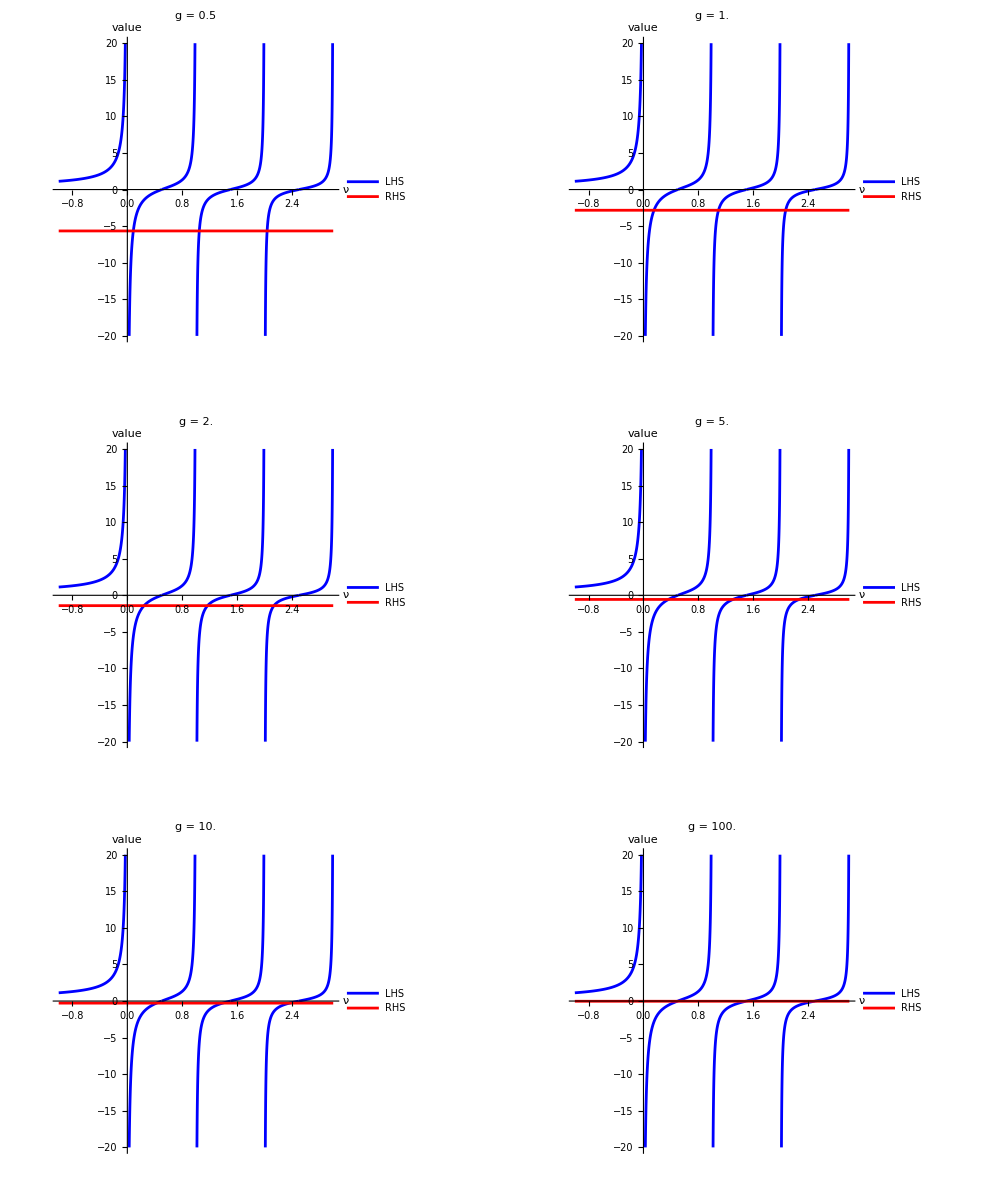

```mathematica
GraphicsGrid[Partition[plots,2],ImageSize->1000]
```

```mathematica
(*Values of g to test*)gValues={0.5,1.0,2.0,5.0,10.0,100.0};
ncom=0;
results=Table[Print["-----------------------------"];
Print["g = ",g];
(*Define functions with this g*)lhs[nu_]:=Gamma[-nu]/Gamma[1/2-nu];
rhs=-2^(3/2)/g;
f[nu_]:=lhs[nu]-rhs;
(*Grid for sign-change detection*)nuGrid=Subdivide[-1,3,3000];
fGrid=f/@nuGrid;
(*Root finding*)solutionsTemp=Reap[
Do[
If[
NumberQ[fGrid[[i]]] && NumberQ[fGrid[[i + 1]]] &&fGrid[[i]]*fGrid[[i + 1]] < 0,           (* sign change detected *)
      root = N[nu /. 
         FindRoot[f[nu] == 0, {nu, nuGrid[[i]], nuGrid[[i + 1]]}, 
         Method -> "Brent"]];
      
      Sow[root];
     ],
    {i, 1, Length[nuGrid] - 1}
   ]
 ][[2, 1]];


solutions=DeleteDuplicates[Round[solutionsTemp,10^-10]]; solutions=N[solutions];
energies=Erel[solutions];
totalenergies=Etotal[ncom,solutions];
Print["ν solutions = ",solutions];
Print["Relative energies = ",energies];
Print["Total energies = ",totalenergies];
<|"g"->g,"nu"->solutions,"energies"->energies,"totalenergies"->totalenergies|>,{g,gValues}]
```

-----------------------------

g = 0.5

ν solutions = {0.08713,1.04858,2.03693}

Relative energies = {0.67426,2.59715,4.57387}

Total energies = {1.17426,3.09715,5.07387}

-----------------------------

g = 1.

ν solutions = {0.153373,1.09353,2.07237}

Relative energies = {0.806746,2.68705,4.64473}

Total energies = {1.30675,3.18705,5.14473}

-----------------------------

g = 2.

ν solutions = {0.243701,1.16948,2.13632}

Relative energies = {0.987402,2.83897,4.77264}

Total energies = {1.4874,3.33897,5.27264}

-----------------------------

g = 5.

ν solutions = {0.36339,1.3036,2.26681}

Relative energies = {1.22678,3.10719,5.03362}

Total energies = {1.72678,3.60719,5.53362}

-----------------------------

g = 10.

ν solutions = {0.425344,1.38885,2.36322}

Relative energies = {1.35069,3.27771,5.22645}

Total energies = {1.85069,3.77771,5.72645}

-----------------------------

g = 100.

ν solutions = {0.492062,1.48808,2.48509}

Relative energies = {1.48412,3.47615,5.47018}

Total energies = {1.98412,3.97615,5.97018}

{<|g→0.5,nu→{0.08713,1.04858,2.03693},energies→{0.67426,2.59715,4.57387},totalenergies→{1.17426,3.09715,5.07387}|>,<|g→1.,nu→{0.153373,1.09353,2.07237},energies→{0.806746,2.68705,4.64473},totalenergies→{1.30675,3.18705,5.14473}|>,<|g→2.,nu→{0.243701,1.16948,2.13632},energies→{0.987402,2.83897,4.77264},totalenergies→{1.4874,3.33897,5.27264}|>,<|g→5.,nu→{0.36339,1.3036,2.26681},energies→{1.22678,3.10719,5.03362},totalenergies→{1.72678,3.60719,5.53362}|>,<|g→10.,nu→{0.425344,1.38885,2.36322},energies→{1.35069,3.27771,5.22645},totalenergies→{1.85069,3.77771,5.72645}|>,<|g→100.,nu→{0.492062,1.48808,2.48509},energies→{1.48412,3.47615,5.47018},totalenergies→{1.98412,3.97615,5.97018}|>}

```mathematica
niceTable=Grid[Prepend[(List@@#)&/@results,{"g","ν solutions","Relative energy","Total energy (ncom=0)"}],Frame->All,Alignment->{Left,Center},ItemSize->All,Spacings->{1,1},ItemStyle->Directive[14]];

niceTable
```

g | ν solutions | Relative energy | Total energy (ncom=0)
0.5 | {0.08713,1.04858,2.03693} | {0.67426,2.59715,4.57387} | {1.17426,3.09715,5.07387}
1. | {0.153373,1.09353,2.07237} | {0.806746,2.68705,4.64473} | {1.30675,3.18705,5.14473}
2. | {0.243701,1.16948,2.13632} | {0.987402,2.83897,4.77264} | {1.4874,3.33897,5.27264}
5. | {0.36339,1.3036,2.26681} | {1.22678,3.10719,5.03362} | {1.72678,3.60719,5.53362}
10. | {0.425344,1.38885,2.36322} | {1.35069,3.27771,5.22645} | {1.85069,3.77771,5.72645}
100. | {0.492062,1.48808,2.48509} | {1.48412,3.47615,5.47018} | {1.98412,3.97615,5.97018}

```mathematica
gValues=Subdivide[0.1,100,300];
ncom=0;
results=Table[
(*Define functions with this g*)lhs[nu_]:=Gamma[-nu]/Gamma[1/2-nu];
rhs=-2^(3/2)/g;
f[nu_]:=lhs[nu]-rhs;
(*Grid for sign-change detection*)nuGrid=Subdivide[-1,3,3000];
fGrid=f/@nuGrid;
(*Root finding*)solutionsTemp=Reap[
Do[
If[
NumberQ[fGrid[[i]]] && NumberQ[fGrid[[i + 1]]] &&fGrid[[i]]*fGrid[[i + 1]] < 0,           (* sign change detected *)
      root = N[nu /. 
         FindRoot[f[nu] == 0, {nu, nuGrid[[i]], nuGrid[[i + 1]]}, 
         Method -> "Brent"]];
      
      Sow[root];
     ],
    {i, 1, Length[nuGrid] - 1}
   ]
 ][[2, 1]];


solutions=DeleteDuplicates[Round[solutionsTemp,10^-10]]; solutions=N[solutions];
energies=Erel[solutions];
totalenergies=Etotal[ncom,solutions];
<|"g"->g,"nu"->solutions,"energies"->energies,"totalenergies"->totalenergies|>,{g,gValues}]
```

{<|g→0.1,nu→{0.0194053,1.00993,2.00747},energies→{0.538811,2.51986,4.51493},totalenergies→{1.03881,3.01986,5.01493}|>,<|g→0.433,nu→{0.0768026,1.04225,2.03205},energies→{0.653605,2.58449,4.56411},totalenergies→{1.15361,3.08449,5.06411}|>,<|g→0.766,nu→{0.124592,1.07302,2.05602},energies→{0.749183,2.64604,4.61204},totalenergies→{1.24918,3.14604,5.11204}|>,<|g→1.099,nu→{0.16451,1.1019,2.07914},energies→{0.829021,2.7038,4.65828},totalenergies→{1.32902,3.2038,5.15828}|>,<|g→1.432,nu→{0.198021,1.1287,2.10125},energies→{0.896041,2.7574,4.7025},totalenergies→{1.39604,3.2574,5.2025}|>,<|g→1.765,nu→{0.226325,1.15335,2.12223},energies→{0.952649,2.80671,4.74446},totalenergies→{1.45265,3.30671,5.24446}|>,<|g→2.098,nu→{0.250394,1.17591,2.14202},energies→{1.00079,2.85181,4.78403},totalenergies→{1.50079,3.35181,5.28403}|>,<|g→2.431,nu→{0.271009,1.19645,2.16058},energies→{1.04202,2.89291,4.82116},totalenergies→{1.54202,3.39291,5.32116}|>,<|g→2.764,nu→{0.288792,1.21513,2.17793},energies→{1.07758,2.93027,4.85586},totalenergies→{1.57758,3.43027,5.35586}|>,<|g→3.097,nu→{0.304238,1.2321,2.1941},energies→{1.10848,2.9642,4.8882},totalenergies→{1.60848,3.4642,5.3882}|>,<|g→3.43,nu→{0.317746,1.24751,2.20914},energies→{1.13549,2.99503,4.91828},totalenergies→{1.63549,3.49503,5.41828}|>,<|g→3.763,nu→{0.329634,1.26153,2.22311},energies→{1.15927,3.02305,4.94623},totalenergies→{1.65927,3.52305,5.44623}|>,<|g→4.096,nu→{0.34016,1.27429,2.23609},energies→{1.18032,3.04857,4.97217},totalenergies→{1.68032,3.54857,5.47217}|>,<|g→4.429,nu→{0.349531,1.28592,2.24813},energies→{1.19906,3.07184,4.99626},totalenergies→{1.69906,3.57184,5.49626}|>,<|g→4.762,nu→{0.357919,1.29655,2.25931},energies→{1.21584,3.09311,5.01862},totalenergies→{1.71584,3.59311,5.51862}|>,<|g→5.095,nu→{0.365464,1.30629,2.2697},energies→{1.23093,3.11258,5.03939},totalenergies→{1.73093,3.61258,5.53939}|>,<|g→5.428,nu→{0.372281,1.31523,2.27935},energies→{1.24456,3.13045,5.0587},totalenergies→{1.74456,3.63045,5.5587}|>,<|g→5.761,nu→{0.378467,1.32345,2.28834},energies→{1.25693,3.14689,5.07668},totalenergies→{1.75693,3.64689,5.57668}|>,<|g→6.094,nu→{0.384103,1.33103,2.29672},energies→{1.26821,3.16205,5.09343},totalenergies→{1.76821,3.66205,5.59343}|>,<|g→6.427,nu→{0.389256,1.33803,2.30453},energies→{1.27851,3.17606,5.10905},totalenergies→{1.77851,3.67606,5.60905}|>,<|g→6.76,nu→{0.393985,1.34452,2.31183},energies→{1.28797,3.18903,5.12365},totalenergies→{1.78797,3.68903,5.62365}|>,<|g→7.093,nu→{0.398337,1.35054,2.31865},energies→{1.29667,3.20107,5.1373},totalenergies→{1.79667,3.70107,5.6373}|>,<|g→7.426,nu→{0.402356,1.35613,2.32504},energies→{1.30471,3.21227,5.15009},totalenergies→{1.80471,3.71227,5.65009}|>,<|g→7.759,nu→{0.406077,1.36135,2.33104},energies→{1.31215,3.2227,5.16208},totalenergies→{1.81215,3.7227,5.66208}|>,<|g→8.092,nu→{0.409531,1.36622,2.33667},energies→{1.31906,3.23245,5.17335},totalenergies→{1.81906,3.73245,5.67335}|>,<|g→8.425,nu→{0.412746,1.37078,2.34197},energies→{1.32549,3.24157,5.18394},totalenergies→{1.82549,3.74157,5.68394}|>,<|g→8.758,nu→{0.415744,1.37505,2.34696},energies→{1.33149,3.25011,5.19392},totalenergies→{1.83149,3.75011,5.69392}|>,<|g→9.091,nu→{0.418548,1.37907,2.35166},energies→{1.3371,3.25813,5.20332},totalenergies→{1.8371,3.75813,5.70332}|>,<|g→9.424,nu→{0.421174,1.38284,2.3561},energies→{1.34235,3.26567,5.21221},totalenergies→{1.84235,3.76567,5.71221}|>,<|g→9.757,nu→{0.423639,1.38639,2.3603},energies→{1.34728,3.27278,5.2206},totalenergies→{1.84728,3.77278,5.7206}|>,<|g→10.09,nu→{0.425957,1.38974,2.36428},energies→{1.35191,3.27948,5.22855},totalenergies→{1.85191,3.77948,5.72855}|>,<|g→10.423,nu→{0.42814,1.39291,2.36804},energies→{1.35628,3.28581,5.23609},totalenergies→{1.85628,3.78581,5.73609}|>,<|g→10.756,nu→{0.4302,1.3959,2.37162},energies→{1.3604,3.2918,5.24323},totalenergies→{1.8604,3.7918,5.74323}|>,<|g→11.089,nu→{0.432147,1.39874,2.37501},energies→{1.36429,3.29748,5.25002},totalenergies→{1.86429,3.79748,5.75002}|>,<|g→11.422,nu→{0.43399,1.40143,2.37824},energies→{1.36798,3.30286,5.25648},totalenergies→{1.86798,3.80286,5.75648}|>,<|g→11.755,nu→{0.435737,1.40399,2.38131},energies→{1.37147,3.30797,5.26262},totalenergies→{1.87147,3.80797,5.76262}|>,<|g→12.088,nu→{0.437394,1.40642,2.38424},energies→{1.37479,3.31283,5.26848},totalenergies→{1.87479,3.81283,5.76848}|>,<|g→12.421,nu→{0.438969,1.40873,2.38703},energies→{1.37794,3.31746,5.27406},totalenergies→{1.87794,3.81746,5.77406}|>,<|g→12.754,nu→{0.440468,1.41093,2.3897},energies→{1.38094,3.32187,5.27939},totalenergies→{1.88094,3.82187,5.77939}|>,<|g→13.087,nu→{0.441896,1.41304,2.39224},energies→{1.38379,3.32607,5.28449},totalenergies→{1.88379,3.82607,5.78449}|>,<|g→13.42,nu→{0.443257,1.41504,2.39468},energies→{1.38651,3.33009,5.28936},totalenergies→{1.88651,3.83009,5.78936}|>,<|g→13.753,nu→{0.444557,1.41696,2.39701},energies→{1.38911,3.33393,5.29402},totalenergies→{1.88911,3.83393,5.79402}|>,<|g→14.086,nu→{0.445799,1.4188,2.39925},energies→{1.3916,3.3376,5.29849},totalenergies→{1.8916,3.8376,5.79849}|>,<|g→14.419,nu→{0.446987,1.42056,2.40139},energies→{1.39397,3.34111,5.30278},totalenergies→{1.89397,3.84111,5.80278}|>,<|g→14.752,nu→{0.448124,1.42224,2.40344},energies→{1.39625,3.34448,5.30689},totalenergies→{1.89625,3.84448,5.80689}|>,<|g→15.085,nu→{0.449215,1.42386,2.40542},energies→{1.39843,3.34772,5.31084},totalenergies→{1.89843,3.84772,5.81084}|>,<|g→15.418,nu→{0.45026,1.42541,2.40732},energies→{1.40052,3.35082,5.31463},totalenergies→{1.90052,3.85082,5.81463}|>,<|g→15.751,nu→{0.451264,1.4269,2.40914},energies→{1.40253,3.3538,5.31828},totalenergies→{1.90253,3.8538,5.81828}|>,<|g→16.084,nu→{0.452228,1.42833,2.4109},energies→{1.40446,3.35667,5.32179},totalenergies→{1.90446,3.85667,5.82179}|>,<|g→16.417,nu→{0.453155,1.42971,2.41259},energies→{1.40631,3.35943,5.32517},totalenergies→{1.90631,3.85943,5.82517}|>,<|g→16.75,nu→{0.454048,1.43104,2.41422},energies→{1.4081,3.36208,5.32843},totalenergies→{1.9081,3.86208,5.82843}|>,<|g→17.083,nu→{0.454907,1.43232,2.41579},energies→{1.40981,3.36464,5.33157},totalenergies→{1.90981,3.86464,5.83157}|>,<|g→17.416,nu→{0.455734,1.43355,2.4173},energies→{1.41147,3.36711,5.33461},totalenergies→{1.91147,3.86711,5.83461}|>,<|g→17.749,nu→{0.456532,1.43474,2.41877},energies→{1.41306,3.36949,5.33753},totalenergies→{1.91306,3.86949,5.83753}|>,<|g→18.082,nu→{0.457302,1.43589,2.42018},energies→{1.4146,3.37178,5.34036},totalenergies→{1.9146,3.87178,5.84036}|>,<|g→18.415,nu→{0.458045,1.437,2.42155},energies→{1.41609,3.374,5.34309},totalenergies→{1.91609,3.874,5.84309}|>,<|g→18.748,nu→{0.458763,1.43807,2.42287},energies→{1.41753,3.37615,5.34573},totalenergies→{1.91753,3.87615,5.84573}|>,<|g→19.081,nu→{0.459457,1.43911,2.42415},energies→{1.41891,3.37822,5.34829},totalenergies→{1.91891,3.87822,5.84829}|>,<|g→19.414,nu→{0.460128,1.44011,2.42538},energies→{1.42026,3.38023,5.35076},totalenergies→{1.92026,3.88023,5.85076}|>,<|g→19.747,nu→{0.460778,1.44108,2.42658},energies→{1.42156,3.38217,5.35316},totalenergies→{1.92156,3.88217,5.85316}|>,<|g→20.08,nu→{0.461406,1.44202,2.42774},energies→{1.42281,3.38405,5.35548},totalenergies→{1.92281,3.88405,5.85548}|>,<|g→20.413,nu→{0.462015,1.44293,2.42887},energies→{1.42403,3.38587,5.35773},totalenergies→{1.92403,3.88587,5.85773}|>,<|g→20.746,nu→{0.462605,1.44382,2.42996},energies→{1.42521,3.38763,5.35992},totalenergies→{1.92521,3.88763,5.85992}|>,<|g→21.079,nu→{0.463177,1.44467,2.43102},energies→{1.42635,3.38935,5.36203},totalenergies→{1.92635,3.88935,5.86203}|>,<|g→21.412,nu→{0.463732,1.4455,2.43204},energies→{1.42746,3.39101,5.36409},totalenergies→{1.92746,3.89101,5.86409}|>,<|g→21.745,nu→{0.464271,1.44631,2.43304},energies→{1.42854,3.39262,5.36608},totalenergies→{1.92854,3.89262,5.86608}|>,<|g→22.078,nu→{0.464793,1.44709,2.43401},energies→{1.42959,3.39419,5.36802},totalenergies→{1.92959,3.89419,5.86802}|>,<|g→22.411,nu→{0.465301,1.44785,2.43495},energies→{1.4306,3.39571,5.36991},totalenergies→{1.9306,3.89571,5.86991}|>,<|g→22.744,nu→{0.465795,1.44859,2.43587},energies→{1.43159,3.39719,5.37174},totalenergies→{1.93159,3.89719,5.87174}|>,<|g→23.077,nu→{0.466274,1.44931,2.43676},energies→{1.43255,3.39863,5.37352},totalenergies→{1.93255,3.89863,5.87352}|>,<|g→23.41,nu→{0.466741,1.45001,2.43763},energies→{1.43348,3.40002,5.37526},totalenergies→{1.93348,3.90002,5.87526}|>,<|g→23.743,nu→{0.467194,1.45069,2.43847},energies→{1.43439,3.40138,5.37694},totalenergies→{1.93439,3.90138,5.87694}|>,<|g→24.076,nu→{0.467636,1.45135,2.43929},energies→{1.43527,3.40271,5.37859},totalenergies→{1.93527,3.90271,5.87859}|>,<|g→24.409,nu→{0.468066,1.452,2.44009},energies→{1.43613,3.404,5.38019},totalenergies→{1.93613,3.904,5.88019}|>,<|g→24.742,nu→{0.468484,1.45263,2.44087},energies→{1.43697,3.40525,5.38175},totalenergies→{1.93697,3.90525,5.88175}|>,<|g→25.075,nu→{0.468892,1.45324,2.44163},energies→{1.43778,3.40648,5.38326},totalenergies→{1.93778,3.90648,5.88326}|>,<|g→25.408,nu→{0.46929,1.45384,2.44237},energies→{1.43858,3.40767,5.38475},totalenergies→{1.93858,3.90767,5.88475}|>,<|g→25.741,nu→{0.469677,1.45442,2.44309},energies→{1.43935,3.40883,5.38619},totalenergies→{1.93935,3.90883,5.88619}|>,<|g→26.074,nu→{0.470055,1.45498,2.4438},energies→{1.44011,3.40997,5.3876},totalenergies→{1.94011,3.90997,5.8876}|>,<|g→26.407,nu→{0.470423,1.45554,2.44449},energies→{1.44085,3.41108,5.38897},totalenergies→{1.94085,3.91108,5.88897}|>,<|g→26.74,nu→{0.470783,1.45608,2.44516},energies→{1.44157,3.41215,5.39032},totalenergies→{1.94157,3.91215,5.89032}|>,<|g→27.073,nu→{0.471134,1.4566,2.44581},energies→{1.44227,3.41321,5.39163},totalenergies→{1.94227,3.91321,5.89163}|>,<|g→27.406,nu→{0.471477,1.45712,2.44645},energies→{1.44295,3.41424,5.39291},totalenergies→{1.94295,3.91424,5.89291}|>,<|g→27.739,nu→{0.471811,1.45762,2.44708},energies→{1.44362,3.41524,5.39416},totalenergies→{1.94362,3.91524,5.89416}|>,<|g→28.072,nu→{0.472138,1.45811,2.44769},energies→{1.44428,3.41623,5.39538},totalenergies→{1.94428,3.91623,5.89538}|>,<|g→28.405,nu→{0.472458,1.45859,2.44829},energies→{1.44492,3.41719,5.39657},totalenergies→{1.94492,3.91719,5.89657}|>,<|g→28.738,nu→{0.47277,1.45906,2.44887},energies→{1.44554,3.41812,5.39774},totalenergies→{1.94554,3.91812,5.89774}|>,<|g→29.071,nu→{0.473075,1.45952,2.44944},energies→{1.44615,3.41904,5.39888},totalenergies→{1.94615,3.91904,5.89888}|>,<|g→29.404,nu→{0.473374,1.45997,2.45},energies→{1.44675,3.41994,5.4},totalenergies→{1.94675,3.91994,5.9}|>,<|g→29.737,nu→{0.473666,1.46041,2.45054},energies→{1.44733,3.42082,5.40109},totalenergies→{1.94733,3.92082,5.90109}|>,<|g→30.07,nu→{0.473951,1.46084,2.45108},energies→{1.4479,3.42167,5.40216},totalenergies→{1.9479,3.92167,5.90216}|>,<|g→30.403,nu→{0.474231,1.46126,2.4516},energies→{1.44846,3.42251,5.4032},totalenergies→{1.94846,3.92251,5.9032}|>,<|g→30.736,nu→{0.474504,1.46167,2.45211},energies→{1.44901,3.42334,5.40423},totalenergies→{1.94901,3.92334,5.90423}|>,<|g→31.069,nu→{0.474772,1.46207,2.45261},energies→{1.44954,3.42414,5.40523},totalenergies→{1.94954,3.92414,5.90523}|>,<|g→31.402,nu→{0.475035,1.46247,2.45311},energies→{1.45007,3.42493,5.40621},totalenergies→{1.95007,3.92493,5.90621}|>,<|g→31.735,nu→{0.475291,1.46285,2.45359},energies→{1.45058,3.4257,5.40717},totalenergies→{1.95058,3.9257,5.90717}|>,<|g→32.068,nu→{0.475543,1.46323,2.45406},energies→{1.45109,3.42646,5.40812},totalenergies→{1.95109,3.92646,5.90812}|>,<|g→32.401,nu→{0.47579,1.4636,2.45452},energies→{1.45158,3.4272,5.40904},totalenergies→{1.95158,3.9272,5.90904}|>,<|g→32.734,nu→{0.476032,1.46396,2.45497},energies→{1.45206,3.42793,5.40995},totalenergies→{1.95206,3.92793,5.90995}|>,<|g→33.067,nu→{0.476268,1.46432,2.45542},energies→{1.45254,3.42864,5.41083},totalenergies→{1.95254,3.92864,5.91083}|>,<|g→33.4,nu→{0.476501,1.46467,2.45585},energies→{1.453,3.42934,5.4117},totalenergies→{1.953,3.92934,5.9117}|>,<|g→33.733,nu→{0.476729,1.46501,2.45628},energies→{1.45346,3.43002,5.41256},totalenergies→{1.95346,3.93002,5.91256}|>,<|g→34.066,nu→{0.476952,1.46535,2.4567},energies→{1.4539,3.4307,5.4134},totalenergies→{1.9539,3.9307,5.9134}|>,<|g→34.399,nu→{0.477171,1.46568,2.45711},energies→{1.45434,3.43136,5.41422},totalenergies→{1.95434,3.93136,5.91422}|>,<|g→34.732,nu→{0.477386,1.466,2.45751},energies→{1.45477,3.432,5.41502},totalenergies→{1.95477,3.932,5.91502}|>,<|g→35.065,nu→{0.477597,1.46632,2.45791},energies→{1.45519,3.43264,5.41582},totalenergies→{1.95519,3.93264,5.91582}|>,<|g→35.398,nu→{0.477805,1.46663,2.4583},energies→{1.45561,3.43326,5.41659},totalenergies→{1.95561,3.93326,5.91659}|>,<|g→35.731,nu→{0.478008,1.46694,2.45868},energies→{1.45602,3.43387,5.41736},totalenergies→{1.95602,3.93387,5.91736}|>,<|g→36.064,nu→{0.478208,1.46724,2.45905},energies→{1.45642,3.43447,5.4181},totalenergies→{1.95642,3.93447,5.9181}|>,<|g→36.397,nu→{0.478404,1.46753,2.45942},energies→{1.45681,3.43506,5.41884},totalenergies→{1.95681,3.93506,5.91884}|>,<|g→36.73,nu→{0.478596,1.46782,2.45978},energies→{1.45719,3.43564,5.41956},totalenergies→{1.95719,3.93564,5.91956}|>,<|g→37.063,nu→{0.478786,1.46811,2.46014},energies→{1.45757,3.43621,5.42027},totalenergies→{1.95757,3.93621,5.92027}|>,<|g→37.396,nu→{0.478971,1.46839,2.46049},energies→{1.45794,3.43677,5.42097},totalenergies→{1.95794,3.93677,5.92097}|>,<|g→37.729,nu→{0.479154,1.46866,2.46083},energies→{1.45831,3.43732,5.42166},totalenergies→{1.95831,3.93732,5.92166}|>,<|g→38.062,nu→{0.479334,1.46893,2.46116},energies→{1.45867,3.43786,5.42233},totalenergies→{1.95867,3.93786,5.92233}|>,<|g→38.395,nu→{0.47951,1.4692,2.4615},energies→{1.45902,3.43839,5.42299},totalenergies→{1.95902,3.93839,5.92299}|>,<|g→38.728,nu→{0.479684,1.46946,2.46182},energies→{1.45937,3.43891,5.42364},totalenergies→{1.95937,3.93891,5.92364}|>,<|g→39.061,nu→{0.479854,1.46971,2.46214},energies→{1.45971,3.43943,5.42428},totalenergies→{1.95971,3.93943,5.92428}|>,<|g→39.394,nu→{0.480022,1.46997,2.46246},energies→{1.46004,3.43993,5.42491},totalenergies→{1.96004,3.93993,5.92491}|>,<|g→39.727,nu→{0.480187,1.47021,2.46277},energies→{1.46037,3.44043,5.42553},totalenergies→{1.96037,3.94043,5.92553}|>,<|g→40.06,nu→{0.480349,1.47046,2.46307},energies→{1.4607,3.44092,5.42614},totalenergies→{1.9607,3.94092,5.92614}|>,<|g→40.393,nu→{0.480509,1.4707,2.46337},energies→{1.46102,3.4414,5.42674},totalenergies→{1.96102,3.9414,5.92674}|>,<|g→40.726,nu→{0.480666,1.47093,2.46367},energies→{1.46133,3.44187,5.42733},totalenergies→{1.96133,3.94187,5.92733}|>,<|g→41.059,nu→{0.480821,1.47117,2.46396},energies→{1.46164,3.44233,5.42791},totalenergies→{1.96164,3.94233,5.92791}|>,<|g→41.392,nu→{0.480973,1.4714,2.46424},energies→{1.46195,3.44279,5.42848},totalenergies→{1.96195,3.94279,5.92848}|>,<|g→41.725,nu→{0.481122,1.47162,2.46452},energies→{1.46224,3.44324,5.42905},totalenergies→{1.96224,3.94324,5.92905}|>,<|g→42.058,nu→{0.48127,1.47184,2.4648},energies→{1.46254,3.44369,5.4296},totalenergies→{1.96254,3.94369,5.9296}|>,<|g→42.391,nu→{0.481415,1.47206,2.46507},energies→{1.46283,3.44412,5.43015},totalenergies→{1.96283,3.94412,5.93015}|>,<|g→42.724,nu→{0.481558,1.47228,2.46534},energies→{1.46312,3.44455,5.43068},totalenergies→{1.96312,3.94455,5.93068}|>,<|g→43.057,nu→{0.481698,1.47249,2.46561},energies→{1.4634,3.44498,5.43121},totalenergies→{1.9634,3.94498,5.93121}|>,<|g→43.39,nu→{0.481837,1.4727,2.46587},energies→{1.46367,3.44539,5.43173},totalenergies→{1.96367,3.94539,5.93173}|>,<|g→43.723,nu→{0.481974,1.4729,2.46612},energies→{1.46395,3.4458,5.43224},totalenergies→{1.96395,3.9458,5.93224}|>,<|g→44.056,nu→{0.482108,1.4731,2.46637},energies→{1.46422,3.44621,5.43275},totalenergies→{1.96422,3.94621,5.93275}|>,<|g→44.389,nu→{0.48224,1.4733,2.46662},energies→{1.46448,3.44661,5.43325},totalenergies→{1.96448,3.94661,5.93325}|>,<|g→44.722,nu→{0.482371,1.4735,2.46687},energies→{1.46474,3.447,5.43374},totalenergies→{1.96474,3.947,5.93374}|>,<|g→45.055,nu→{0.4825,1.47369,2.46711},energies→{1.465,3.44739,5.43422},totalenergies→{1.965,3.94739,5.93422}|>,<|g→45.388,nu→{0.482626,1.47388,2.46735},energies→{1.46525,3.44777,5.4347},totalenergies→{1.96525,3.94777,5.9347}|>,<|g→45.721,nu→{0.482751,1.47407,2.46758},energies→{1.4655,3.44814,5.43517},totalenergies→{1.9655,3.94814,5.93517}|>,<|g→46.054,nu→{0.482875,1.47426,2.46781},energies→{1.46575,3.44851,5.43563},totalenergies→{1.96575,3.94851,5.93563}|>,<|g→46.387,nu→{0.482996,1.47444,2.46804},energies→{1.46599,3.44888,5.43609},totalenergies→{1.96599,3.94888,5.93609}|>,<|g→46.72,nu→{0.483116,1.47462,2.46827},energies→{1.46623,3.44924,5.43654},totalenergies→{1.96623,3.94924,5.93654}|>,<|g→47.053,nu→{0.483234,1.4748,2.46849},energies→{1.46647,3.44959,5.43698},totalenergies→{1.96647,3.94959,5.93698}|>,<|g→47.386,nu→{0.48335,1.47497,2.46871},energies→{1.4667,3.44995,5.43742},totalenergies→{1.9667,3.94995,5.93742}|>,<|g→47.719,nu→{0.483465,1.47515,2.46892},energies→{1.46693,3.45029,5.43785},totalenergies→{1.96693,3.95029,5.93785}|>,<|g→48.052,nu→{0.483578,1.47532,2.46914},energies→{1.46716,3.45063,5.43827},totalenergies→{1.96716,3.95063,5.93827}|>,<|g→48.385,nu→{0.48369,1.47548,2.46935},energies→{1.46738,3.45097,5.43869},totalenergies→{1.96738,3.95097,5.93869}|>,<|g→48.718,nu→{0.4838,1.47565,2.46955},energies→{1.4676,3.4513,5.43911},totalenergies→{1.9676,3.9513,5.93911}|>,<|g→49.051,nu→{0.483909,1.47581,2.46976},energies→{1.46782,3.45163,5.43952},totalenergies→{1.96782,3.95163,5.93952}|>,<|g→49.384,nu→{0.484016,1.47597,2.46996},energies→{1.46803,3.45195,5.43992},totalenergies→{1.96803,3.95195,5.93992}|>,<|g→49.717,nu→{0.484122,1.47613,2.47016},energies→{1.46824,3.45227,5.44032},totalenergies→{1.96824,3.95227,5.94032}|>,<|g→50.05,nu→{0.484226,1.47629,2.47036},energies→{1.46845,3.45258,5.44071},totalenergies→{1.96845,3.95258,5.94071}|>,<|g→50.383,nu→{0.484329,1.47645,2.47055},energies→{1.46866,3.45289,5.4411},totalenergies→{1.96866,3.95289,5.9411}|>,<|g→50.716,nu→{0.484431,1.4766,2.47074},energies→{1.46886,3.4532,5.44148},totalenergies→{1.96886,3.9532,5.94148}|>,<|g→51.049,nu→{0.484531,1.47675,2.47093},energies→{1.46906,3.4535,5.44186},totalenergies→{1.96906,3.9535,5.94186}|>,<|g→51.382,nu→{0.484631,1.4769,2.47112},energies→{1.46926,3.4538,5.44223},totalenergies→{1.96926,3.9538,5.94223}|>,<|g→51.715,nu→{0.484728,1.47705,2.4713},energies→{1.46946,3.45409,5.4426},totalenergies→{1.96946,3.95409,5.9426}|>,<|g→52.048,nu→{0.484825,1.47719,2.47148},energies→{1.46965,3.45438,5.44296},totalenergies→{1.96965,3.95438,5.94296}|>,<|g→52.381,nu→{0.484921,1.47734,2.47166},energies→{1.46984,3.45467,5.44332},totalenergies→{1.96984,3.95467,5.94332}|>,<|g→52.714,nu→{0.485015,1.47748,2.47184},energies→{1.47003,3.45495,5.44368},totalenergies→{1.97003,3.95495,5.94368}|>,<|g→53.047,nu→{0.485108,1.47762,2.47201},energies→{1.47022,3.45523,5.44403},totalenergies→{1.97022,3.95523,5.94403}|>,<|g→53.38,nu→{0.4852,1.47776,2.47219},energies→{1.4704,3.45551,5.44437},totalenergies→{1.9704,3.95551,5.94437}|>,<|g→53.713,nu→{0.485291,1.47789,2.47236},energies→{1.47058,3.45578,5.44471},totalenergies→{1.97058,3.95578,5.94471}|>,<|g→54.046,nu→{0.48538,1.47803,2.47253},energies→{1.47076,3.45605,5.44505},totalenergies→{1.97076,3.95605,5.94505}|>,<|g→54.379,nu→{0.485469,1.47816,2.47269},energies→{1.47094,3.45632,5.44538},totalenergies→{1.97094,3.95632,5.94538}|>,<|g→54.712,nu→{0.485556,1.47829,2.47286},energies→{1.47111,3.45658,5.44571},totalenergies→{1.97111,3.95658,5.94571}|>,<|g→55.045,nu→{0.485643,1.47842,2.47302},energies→{1.47129,3.45684,5.44604},totalenergies→{1.97129,3.95684,5.94604}|>,<|g→55.378,nu→{0.485728,1.47855,2.47318},energies→{1.47146,3.4571,5.44636},totalenergies→{1.97146,3.9571,5.94636}|>,<|g→55.711,nu→{0.485813,1.47868,2.47334},energies→{1.47163,3.45736,5.44668},totalenergies→{1.97163,3.95736,5.94668}|>,<|g→56.044,nu→{0.485896,1.4788,2.4735},energies→{1.47179,3.45761,5.44699},totalenergies→{1.97179,3.95761,5.94699}|>,<|g→56.377,nu→{0.485979,1.47893,2.47365},energies→{1.47196,3.45786,5.4473},totalenergies→{1.97196,3.95786,5.9473}|>,<|g→56.71,nu→{0.48606,1.47905,2.4738},energies→{1.47212,3.4581,5.44761},totalenergies→{1.97212,3.9581,5.94761}|>,<|g→57.043,nu→{0.486141,1.47917,2.47396},energies→{1.47228,3.45834,5.44791},totalenergies→{1.97228,3.95834,5.94791}|>,<|g→57.376,nu→{0.48622,1.47929,2.47411},energies→{1.47244,3.45858,5.44821},totalenergies→{1.97244,3.95858,5.94821}|>,<|g→57.709,nu→{0.486299,1.47941,2.47425},energies→{1.4726,3.45882,5.44851},totalenergies→{1.9726,3.95882,5.94851}|>,<|g→58.042,nu→{0.486377,1.47953,2.4744},energies→{1.47275,3.45905,5.4488},totalenergies→{1.97275,3.95905,5.9488}|>,<|g→58.375,nu→{0.486454,1.47964,2.47454},energies→{1.47291,3.45929,5.44909},totalenergies→{1.97291,3.95929,5.94909}|>,<|g→58.708,nu→{0.48653,1.47976,2.47469},energies→{1.47306,3.45951,5.44937},totalenergies→{1.97306,3.95951,5.94937}|>,<|g→59.041,nu→{0.486605,1.47987,2.47483},energies→{1.47321,3.45974,5.44966},totalenergies→{1.97321,3.95974,5.94966}|>,<|g→59.374,nu→{0.48668,1.47998,2.47497},energies→{1.47336,3.45996,5.44994},totalenergies→{1.97336,3.95996,5.94994}|>,<|g→59.707,nu→{0.486753,1.48009,2.47511},energies→{1.47351,3.46019,5.45021},totalenergies→{1.97351,3.96019,5.95021}|>,<|g→60.04,nu→{0.486826,1.4802,2.47524},energies→{1.47365,3.46041,5.45049},totalenergies→{1.97365,3.96041,5.95049}|>,<|g→60.373,nu→{0.486898,1.48031,2.47538},energies→{1.4738,3.46062,5.45076},totalenergies→{1.9738,3.96062,5.95076}|>,<|g→60.706,nu→{0.486969,1.48042,2.47551},energies→{1.47394,3.46084,5.45103},totalenergies→{1.97394,3.96084,5.95103}|>,<|g→61.039,nu→{0.48704,1.48052,2.47565},energies→{1.47408,3.46105,5.45129},totalenergies→{1.97408,3.96105,5.95129}|>,<|g→61.372,nu→{0.487109,1.48063,2.47578},energies→{1.47422,3.46126,5.45155},totalenergies→{1.97422,3.96126,5.95155}|>,<|g→61.705,nu→{0.487178,1.48073,2.47591},energies→{1.47436,3.46147,5.45181},totalenergies→{1.97436,3.96147,5.95181}|>,<|g→62.038,nu→{0.487247,1.48084,2.47604},energies→{1.47449,3.46167,5.45207},totalenergies→{1.97449,3.96167,5.95207}|>,<|g→62.371,nu→{0.487314,1.48094,2.47616},energies→{1.47463,3.46187,5.45232},totalenergies→{1.97463,3.96187,5.95232}|>,<|g→62.704,nu→{0.487381,1.48104,2.47629},energies→{1.47476,3.46207,5.45258},totalenergies→{1.97476,3.96207,5.95258}|>,<|g→63.037,nu→{0.487447,1.48114,2.47641},energies→{1.47489,3.46227,5.45282},totalenergies→{1.97489,3.96227,5.95282}|>,<|g→63.37,nu→{0.487512,1.48124,2.47653},energies→{1.47502,3.46247,5.45307},totalenergies→{1.97502,3.96247,5.95307}|>,<|g→63.703,nu→{0.487577,1.48133,2.47666},energies→{1.47515,3.46266,5.45331},totalenergies→{1.97515,3.96266,5.95331}|>,<|g→64.036,nu→{0.487641,1.48143,2.47678},energies→{1.47528,3.46286,5.45355},totalenergies→{1.97528,3.96286,5.95355}|>,<|g→64.369,nu→{0.487704,1.48152,2.4769},energies→{1.47541,3.46305,5.45379},totalenergies→{1.97541,3.96305,5.95379}|>,<|g→64.702,nu→{0.487767,1.48162,2.47701},energies→{1.47553,3.46324,5.45403},totalenergies→{1.97553,3.96324,5.95403}|>,<|g→65.035,nu→{0.487829,1.48171,2.47713},energies→{1.47566,3.46342,5.45426},totalenergies→{1.97566,3.96342,5.95426}|>,<|g→65.368,nu→{0.487891,1.4818,2.47725},energies→{1.47578,3.46361,5.45449},totalenergies→{1.97578,3.96361,5.95449}|>,<|g→65.701,nu→{0.487952,1.4819,2.47736},energies→{1.4759,3.46379,5.45472},totalenergies→{1.9759,3.96379,5.95472}|>,<|g→66.034,nu→{0.488012,1.48199,2.47747},energies→{1.47602,3.46397,5.45495},totalenergies→{1.97602,3.96397,5.95495}|>,<|g→66.367,nu→{0.488072,1.48208,2.47759},energies→{1.47614,3.46415,5.45517},totalenergies→{1.97614,3.96415,5.95517}|>,<|g→66.7,nu→{0.488131,1.48217,2.4777},energies→{1.47626,3.46433,5.4554},totalenergies→{1.97626,3.96433,5.9554}|>,<|g→67.033,nu→{0.488189,1.48225,2.47781},energies→{1.47638,3.46451,5.45562},totalenergies→{1.97638,3.96451,5.95562}|>,<|g→67.366,nu→{0.488247,1.48234,2.47792},energies→{1.47649,3.46468,5.45583},totalenergies→{1.97649,3.96468,5.95583}|>,<|g→67.699,nu→{0.488304,1.48243,2.47802},energies→{1.47661,3.46485,5.45605},totalenergies→{1.97661,3.96485,5.95605}|>,<|g→68.032,nu→{0.488361,1.48251,2.47813},energies→{1.47672,3.46502,5.45626},totalenergies→{1.97672,3.96502,5.95626}|>,<|g→68.365,nu→{0.488417,1.4826,2.47824},energies→{1.47683,3.46519,5.45647},totalenergies→{1.97683,3.96519,5.95647}|>,<|g→68.698,nu→{0.488473,1.48268,2.47834},energies→{1.47695,3.46536,5.45668},totalenergies→{1.97695,3.96536,5.95668}|>,<|g→69.031,nu→{0.488528,1.48276,2.47845},energies→{1.47706,3.46553,5.45689},totalenergies→{1.97706,3.96553,5.95689}|>,<|g→69.364,nu→{0.488583,1.48285,2.47855},energies→{1.47717,3.46569,5.4571},totalenergies→{1.97717,3.96569,5.9571}|>,<|g→69.697,nu→{0.488637,1.48293,2.47865},energies→{1.47727,3.46585,5.4573},totalenergies→{1.97727,3.96585,5.9573}|>,<|g→70.03,nu→{0.488691,1.48301,2.47875},energies→{1.47738,3.46602,5.4575},totalenergies→{1.97738,3.96602,5.9575}|>,<|g→70.363,nu→{0.488744,1.48309,2.47885},energies→{1.47749,3.46617,5.4577},totalenergies→{1.97749,3.96617,5.9577}|>,<|g→70.696,nu→{0.488796,1.48317,2.47895},energies→{1.47759,3.46633,5.4579},totalenergies→{1.97759,3.96633,5.9579}|>,<|g→71.029,nu→{0.488848,1.48324,2.47905},energies→{1.4777,3.46649,5.4581},totalenergies→{1.9777,3.96649,5.9581}|>,<|g→71.362,nu→{0.4889,1.48332,2.47914},energies→{1.4778,3.46665,5.45829},totalenergies→{1.9778,3.96665,5.95829}|>,<|g→71.695,nu→{0.488951,1.4834,2.47924},energies→{1.4779,3.4668,5.45848},totalenergies→{1.9779,3.9668,5.95848}|>,<|g→72.028,nu→{0.489002,1.48348,2.47934},energies→{1.478,3.46695,5.45867},totalenergies→{1.978,3.96695,5.95867}|>,<|g→72.361,nu→{0.489052,1.48355,2.47943},energies→{1.4781,3.4671,5.45886},totalenergies→{1.9781,3.9671,5.95886}|>,<|g→72.694,nu→{0.489102,1.48363,2.47952},energies→{1.4782,3.46725,5.45905},totalenergies→{1.9782,3.96725,5.95905}|>,<|g→73.027,nu→{0.489151,1.4837,2.47962},energies→{1.4783,3.4674,5.45923},totalenergies→{1.9783,3.9674,5.95923}|>,<|g→73.36,nu→{0.4892,1.48377,2.47971},energies→{1.4784,3.46755,5.45942},totalenergies→{1.9784,3.96755,5.95942}|>,<|g→73.693,nu→{0.489249,1.48385,2.4798},energies→{1.4785,3.46769,5.4596},totalenergies→{1.9785,3.96769,5.9596}|>,<|g→74.026,nu→{0.489297,1.48392,2.47989},energies→{1.47859,3.46784,5.45978},totalenergies→{1.97859,3.96784,5.95978}|>,<|g→74.359,nu→{0.489344,1.48399,2.47998},energies→{1.47869,3.46798,5.45996},totalenergies→{1.97869,3.96798,5.95996}|>,<|g→74.692,nu→{0.489391,1.48406,2.48007},energies→{1.47878,3.46812,5.46014},totalenergies→{1.97878,3.96812,5.96014}|>,<|g→75.025,nu→{0.489438,1.48413,2.48016},energies→{1.47888,3.46826,5.46031},totalenergies→{1.97888,3.96826,5.96031}|>,<|g→75.358,nu→{0.489484,1.4842,2.48024},energies→{1.47897,3.4684,5.46049},totalenergies→{1.97897,3.9684,5.96049}|>,<|g→75.691,nu→{0.48953,1.48427,2.48033},energies→{1.47906,3.46854,5.46066},totalenergies→{1.97906,3.96854,5.96066}|>,<|g→76.024,nu→{0.489576,1.48434,2.48042},energies→{1.47915,3.46868,5.46083},totalenergies→{1.97915,3.96868,5.96083}|>,<|g→76.357,nu→{0.489621,1.48441,2.4805},energies→{1.47924,3.46881,5.461},totalenergies→{1.97924,3.96881,5.961}|>,<|g→76.69,nu→{0.489666,1.48447,2.48059},energies→{1.47933,3.46895,5.46117},totalenergies→{1.97933,3.96895,5.96117}|>,<|g→77.023,nu→{0.48971,1.48454,2.48067},energies→{1.47942,3.46908,5.46134},totalenergies→{1.97942,3.96908,5.96134}|>,<|g→77.356,nu→{0.489754,1.48461,2.48075},energies→{1.47951,3.46921,5.4615},totalenergies→{1.97951,3.96921,5.9615}|>,<|g→77.689,nu→{0.489798,1.48467,2.48083},energies→{1.4796,3.46935,5.46167},totalenergies→{1.9796,3.96935,5.96167}|>,<|g→78.022,nu→{0.489841,1.48474,2.48091},energies→{1.47968,3.46948,5.46183},totalenergies→{1.97968,3.96948,5.96183}|>,<|g→78.355,nu→{0.489884,1.4848,2.481},energies→{1.47977,3.4696,5.46199},totalenergies→{1.97977,3.9696,5.96199}|>,<|g→78.688,nu→{0.489926,1.48487,2.48108},energies→{1.47985,3.46973,5.46215},totalenergies→{1.97985,3.96973,5.96215}|>,<|g→79.021,nu→{0.489969,1.48493,2.48115},energies→{1.47994,3.46986,5.46231},totalenergies→{1.97994,3.96986,5.96231}|>,<|g→79.354,nu→{0.49001,1.48499,2.48123},energies→{1.48002,3.46999,5.46247},totalenergies→{1.98002,3.96999,5.96247}|>,<|g→79.687,nu→{0.490052,1.48505,2.48131},energies→{1.4801,3.47011,5.46262},totalenergies→{1.9801,3.97011,5.96262}|>,<|g→80.02,nu→{0.490093,1.48512,2.48139},energies→{1.48019,3.47023,5.46278},totalenergies→{1.98019,3.97023,5.96278}|>,<|g→80.353,nu→{0.490134,1.48518,2.48147},energies→{1.48027,3.47036,5.46293},totalenergies→{1.98027,3.97036,5.96293}|>,<|g→80.686,nu→{0.490174,1.48524,2.48154},energies→{1.48035,3.47048,5.46308},totalenergies→{1.98035,3.97048,5.96308}|>,<|g→81.019,nu→{0.490214,1.4853,2.48162},energies→{1.48043,3.4706,5.46323},totalenergies→{1.98043,3.9706,5.96323}|>,<|g→81.352,nu→{0.490254,1.48536,2.48169},energies→{1.48051,3.47072,5.46338},totalenergies→{1.98051,3.97072,5.96338}|>,<|g→81.685,nu→{0.490294,1.48542,2.48177},energies→{1.48059,3.47084,5.46353},totalenergies→{1.98059,3.97084,5.96353}|>,<|g→82.018,nu→{0.490333,1.48548,2.48184},energies→{1.48067,3.47095,5.46368},totalenergies→{1.98067,3.97095,5.96368}|>,<|g→82.351,nu→{0.490372,1.48554,2.48191},energies→{1.48074,3.47107,5.46382},totalenergies→{1.98074,3.97107,5.96382}|>,<|g→82.684,nu→{0.49041,1.48559,2.48198},energies→{1.48082,3.47119,5.46397},totalenergies→{1.98082,3.97119,5.96397}|>,<|g→83.017,nu→{0.490448,1.48565,2.48206},energies→{1.4809,3.4713,5.46411},totalenergies→{1.9809,3.9713,5.96411}|>,<|g→83.35,nu→{0.490486,1.48571,2.48213},energies→{1.48097,3.47142,5.46426},totalenergies→{1.98097,3.97142,5.96426}|>,<|g→83.683,nu→{0.490524,1.48576,2.4822},energies→{1.48105,3.47153,5.4644},totalenergies→{1.98105,3.97153,5.9644}|>,<|g→84.016,nu→{0.490561,1.48582,2.48227},energies→{1.48112,3.47164,5.46454},totalenergies→{1.98112,3.97164,5.96454}|>,<|g→84.349,nu→{0.490598,1.48588,2.48234},energies→{1.4812,3.47175,5.46468},totalenergies→{1.9812,3.97175,5.96468}|>,<|g→84.682,nu→{0.490635,1.48593,2.48241},energies→{1.48127,3.47186,5.46482},totalenergies→{1.98127,3.97186,5.96482}|>,<|g→85.015,nu→{0.490671,1.48599,2.48248},energies→{1.48134,3.47197,5.46495},totalenergies→{1.98134,3.97197,5.96495}|>,<|g→85.348,nu→{0.490707,1.48604,2.48254},energies→{1.48141,3.47208,5.46509},totalenergies→{1.98141,3.97208,5.96509}|>,<|g→85.681,nu→{0.490743,1.4861,2.48261},energies→{1.48149,3.47219,5.46522},totalenergies→{1.98149,3.97219,5.96522}|>,<|g→86.014,nu→{0.490779,1.48615,2.48268},energies→{1.48156,3.4723,5.46536},totalenergies→{1.98156,3.9723,5.96536}|>,<|g→86.347,nu→{0.490814,1.4862,2.48275},energies→{1.48163,3.4724,5.46549},totalenergies→{1.98163,3.9724,5.96549}|>,<|g→86.68,nu→{0.490849,1.48625,2.48281},energies→{1.4817,3.47251,5.46562},totalenergies→{1.9817,3.97251,5.96562}|>,<|g→87.013,nu→{0.490884,1.48631,2.48288},energies→{1.48177,3.47261,5.46575},totalenergies→{1.98177,3.97261,5.96575}|>,<|g→87.346,nu→{0.490919,1.48636,2.48294},energies→{1.48184,3.47272,5.46588},totalenergies→{1.98184,3.97272,5.96588}|>,<|g→87.679,nu→{0.490953,1.48641,2.48301},energies→{1.48191,3.47282,5.46601},totalenergies→{1.98191,3.97282,5.96601}|>,<|g→88.012,nu→{0.490987,1.48646,2.48307},energies→{1.48197,3.47292,5.46614},totalenergies→{1.98197,3.97292,5.96614}|>,<|g→88.345,nu→{0.491021,1.48651,2.48313},energies→{1.48204,3.47302,5.46627},totalenergies→{1.98204,3.97302,5.96627}|>,<|g→88.678,nu→{0.491054,1.48656,2.4832},energies→{1.48211,3.47313,5.46639},totalenergies→{1.98211,3.97313,5.96639}|>,<|g→89.011,nu→{0.491088,1.48661,2.48326},energies→{1.48218,3.47323,5.46652},totalenergies→{1.98218,3.97323,5.96652}|>,<|g→89.344,nu→{0.491121,1.48666,2.48332},energies→{1.48224,3.47332,5.46664},totalenergies→{1.98224,3.97332,5.96664}|>,<|g→89.677,nu→{0.491153,1.48671,2.48338},energies→{1.48231,3.47342,5.46677},totalenergies→{1.98231,3.97342,5.96677}|>,<|g→90.01,nu→{0.491186,1.48676,2.48344},energies→{1.48237,3.47352,5.46689},totalenergies→{1.98237,3.97352,5.96689}|>,<|g→90.343,nu→{0.491218,1.48681,2.4835},energies→{1.48244,3.47362,5.46701},totalenergies→{1.98244,3.97362,5.96701}|>,<|g→90.676,nu→{0.49125,1.48686,2.48356},energies→{1.4825,3.47371,5.46713},totalenergies→{1.9825,3.97371,5.96713}|>,<|g→91.009,nu→{0.491282,1.48691,2.48362},energies→{1.48256,3.47381,5.46725},totalenergies→{1.98256,3.97381,5.96725}|>,<|g→91.342,nu→{0.491314,1.48695,2.48368},energies→{1.48263,3.47391,5.46737},totalenergies→{1.98263,3.97391,5.96737}|>,<|g→91.675,nu→{0.491345,1.487,2.48374},energies→{1.48269,3.474,5.46749},totalenergies→{1.98269,3.974,5.96749}|>,<|g→92.008,nu→{0.491376,1.48705,2.4838},energies→{1.48275,3.47409,5.4676},totalenergies→{1.98275,3.97409,5.9676}|>,<|g→92.341,nu→{0.491407,1.48709,2.48386},energies→{1.48281,3.47419,5.46772},totalenergies→{1.98281,3.97419,5.96772}|>,<|g→92.674,nu→{0.491438,1.48714,2.48392},energies→{1.48288,3.47428,5.46784},totalenergies→{1.98288,3.97428,5.96784}|>,<|g→93.007,nu→{0.491468,1.48719,2.48397},energies→{1.48294,3.47437,5.46795},totalenergies→{1.98294,3.97437,5.96795}|>,<|g→93.34,nu→{0.491499,1.48723,2.48403},energies→{1.483,3.47446,5.46806},totalenergies→{1.983,3.97446,5.96806}|>,<|g→93.673,nu→{0.491529,1.48728,2.48409},energies→{1.48306,3.47455,5.46818},totalenergies→{1.98306,3.97455,5.96818}|>,<|g→94.006,nu→{0.491558,1.48732,2.48414},energies→{1.48312,3.47464,5.46829},totalenergies→{1.98312,3.97464,5.96829}|>,<|g→94.339,nu→{0.491588,1.48737,2.4842},energies→{1.48318,3.47473,5.4684},totalenergies→{1.98318,3.97473,5.9684}|>,<|g→94.672,nu→{0.491618,1.48741,2.48426},energies→{1.48324,3.47482,5.46851},totalenergies→{1.98324,3.97482,5.96851}|>,<|g→95.005,nu→{0.491647,1.48745,2.48431},energies→{1.48329,3.47491,5.46862},totalenergies→{1.98329,3.97491,5.96862}|>,<|g→95.338,nu→{0.491676,1.4875,2.48437},energies→{1.48335,3.47499,5.46873},totalenergies→{1.98335,3.97499,5.96873}|>,<|g→95.671,nu→{0.491705,1.48754,2.48442},energies→{1.48341,3.47508,5.46884},totalenergies→{1.98341,3.97508,5.96884}|>,<|g→96.004,nu→{0.491733,1.48758,2.48447},energies→{1.48347,3.47517,5.46895},totalenergies→{1.98347,3.97517,5.96895}|>,<|g→96.337,nu→{0.491762,1.48763,2.48453},energies→{1.48352,3.47525,5.46905},totalenergies→{1.98352,3.97525,5.96905}|>,<|g→96.67,nu→{0.49179,1.48767,2.48458},energies→{1.48358,3.47534,5.46916},totalenergies→{1.98358,3.97534,5.96916}|>,<|g→97.003,nu→{0.491818,1.48771,2.48463},energies→{1.48364,3.47542,5.46926},totalenergies→{1.98364,3.97542,5.96926}|>,<|g→97.336,nu→{0.491846,1.48775,2.48468},energies→{1.48369,3.47551,5.46937},totalenergies→{1.98369,3.97551,5.96937}|>,<|g→97.669,nu→{0.491873,1.48779,2.48474},energies→{1.48375,3.47559,5.46947},totalenergies→{1.98375,3.97559,5.96947}|>,<|g→98.002,nu→{0.491901,1.48784,2.48479},energies→{1.4838,3.47567,5.46958},totalenergies→{1.9838,3.97567,5.96958}|>,<|g→98.335,nu→{0.491928,1.48788,2.48484},energies→{1.48386,3.47575,5.46968},totalenergies→{1.98386,3.97575,5.96968}|>,<|g→98.668,nu→{0.491955,1.48792,2.48489},energies→{1.48391,3.47583,5.46978},totalenergies→{1.98391,3.97583,5.96978}|>,<|g→99.001,nu→{0.491982,1.48796,2.48494},energies→{1.48396,3.47592,5.46988},totalenergies→{1.98396,3.97592,5.96988}|>,<|g→99.334,nu→{0.492009,1.488,2.48499},energies→{1.48402,3.476,5.46998},totalenergies→{1.98402,3.976,5.96998}|>,<|g→99.667,nu→{0.492035,1.48804,2.48504},energies→{1.48407,3.47608,5.47008},totalenergies→{1.98407,3.97608,5.97008}|>,<|g→100.,nu→{0.492062,1.48808,2.48509},energies→{1.48412,3.47615,5.47018},totalenergies→{1.98412,3.97615,5.97018}|>}

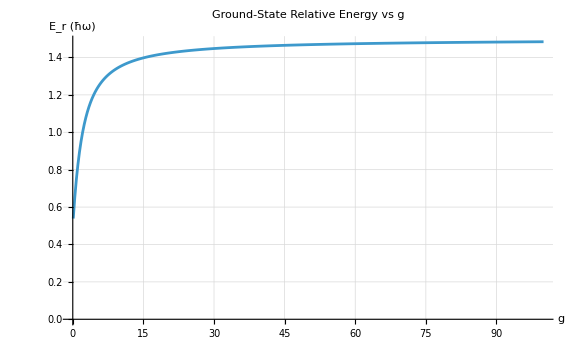

```mathematica
relPlotData={#["g"],Min[#["energies"]]}&/@results;

ListLinePlot[relPlotData,AxesLabel->{"g","E_r (ħω)"},PlotLabel->"Ground-State Relative Energy vs g",GridLines->Automatic,PlotRange->All,ImageSize->Large]
```

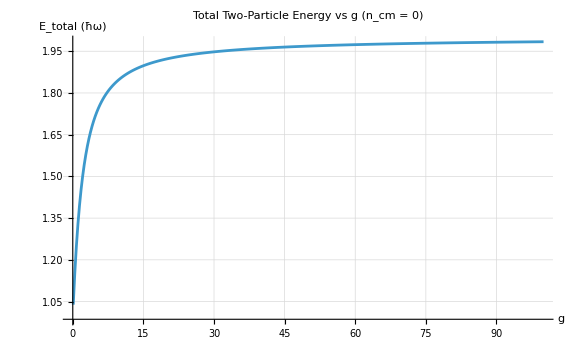

```mathematica
totalPlotData={#["g"],Min[#["totalenergies"]]}&/@results;

ListLinePlot[totalPlotData,AxesLabel->{"g","E_total  (ħω)"},PlotLabel->Style["Total Two-Particle Energy vs g (n_cm = "<>ToString[ncom]<>")",14,Bold],GridLines->Automatic,PlotRange->All,ImageSize->Large]
```

```mathematica
gValues=Subdivide[0.1,50,300];
ncom={0,1,2,3,4};
results=Table[
(*Define functions with this g*)lhs[nu_]:=Gamma[-nu]/Gamma[1/2-nu];
rhs=-2^(3/2)/g;
f[nu_]:=lhs[nu]-rhs;
(*Grid for sign-change detection*)nuGrid=Subdivide[-1,3,3000];
fGrid=f/@nuGrid;
(*Root finding*)solutionsTemp=Reap[
Do[
If[
NumberQ[fGrid[[i]]] && NumberQ[fGrid[[i + 1]]] &&fGrid[[i]]*fGrid[[i + 1]] < 0,           (* sign change detected *)
      root = N[nu /. 
         FindRoot[f[nu] == 0, {nu, nuGrid[[i]], nuGrid[[i + 1]]}, 
         Method -> "Brent"]];
      
      Sow[root];
     ],
    {i, 1, Length[nuGrid] - 1}
   ]
 ][[2, 1]];


solutions=DeleteDuplicates[Round[solutionsTemp,10^-10]]; solutions=N[solutions];
energies=Erel[solutions];
totalenergies=Table[Etotal[n,nu],{n,ncom},{nu,solutions}];
<|"g"->g,"nu"->solutions,"energies"->energies,"totalenergies"->totalenergies|>,{g,gValues}]
```

```mathematica
Dimensions[results[[1,"totalenergies"]]]
```

{5,3}

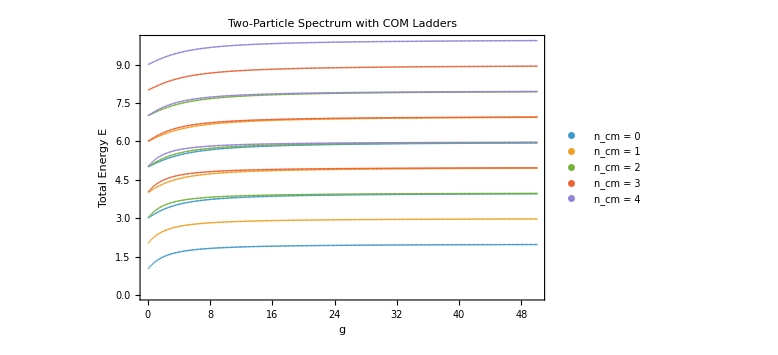

```mathematica
coloredSpectrum=Table[Flatten[Table[{results[[k,"g"]],results[[k,"totalenergies"]][[n,m]]},{k,Length[results]},{m,Length[results[[k,"totalenergies"]][[n]]]}],1],{n,5}];

ListPlot[coloredSpectrum,Frame->True,FrameLabel->{"g","Total Energy E"},PlotRange->All,PlotLegends->("n_cm = "<>ToString[#]&/@Range[0,4]),PlotStyle->PointSize[0.002],PlotLabel->Style["Two-Particle Spectrum with COM Ladders",14,Bold],ImageSize->Large]
```